```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma[a_]=gamma0+gammap0(1/a-1);
elinder[z_] = Sqrt[om(1+z)^3 + (1-om)(1+z)^(3(1 + w0linder + w1linder))Exp[3 w1linder (1/(1+z) - 1)]];
w0linder=-1.29;
w1linder= 2.84;
e[a_]:=elinder[1/a-1]
```

```mathematica
om=0.3;
gamma0=0.55;
gammap0=-0.01;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, f[0.01] == 1}, f, {a,0.01, 1}];
flinder[a_]=f[a]/.Flatten[sol]
```

InterpolatingFunction[…][a]

```mathematica
gammalinder[a_]:=Log[flinder[a]]/Log[omegam[a]]
```

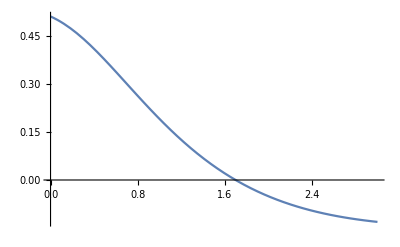

```mathematica
gammaz[z_]:=gammalinder[1/(z+1)]
Plot[gammaz[z],{z,0,3}]
```

```mathematica
points=Table[{z,gammaz[z]},{z,0,0.5,0.01}];
```

```mathematica
Fit[points, {1,z,z^2},z]
```

```mathematica
0.5101562235765528-0.16841376133028285 z-0.2130799011130818 z^2
fit2=Plot[0.5101562235765528-0.16841376133028285* z-0.2130799011130818* z^2,{z,0,3}, PlotStyle->Blue];
```

0.510156-0.168414 z-0.21308 z^2

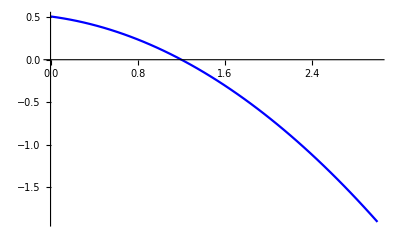

```mathematica
fit2
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```